# Example 5.14 p138

We rewrote the function x^(α-1)/(1+x) as below to get the branch cut lined up on the real axis.

```mathematica
f[α_][z_]:=ⅇ^((α-1)(Log[-z]-ⅈ π))/(1+z)
TabView[
{"6"->ComplexPlot3D[f[6][z],{z, 2}],
"2"->ComplexPlot3D[f[2][z],{z, 2},PlotRange->{0,23}],
"1/3"->ComplexPlot3D[f[1/3][z],{z, 2},
PlotRange->{0,23}],
"-1"->ComplexPlot3D[f[-1][z],{z, 2},
PlotRange->{0,23}],
"-1.562"->ComplexPlot3D[f[-1.562][z],{z, 2},
PlotRange->{0,23}],
"-1.5"->ComplexPlot3D[f[-1.5][z],{z, 2},
PlotRange->{0,23}],
"-3/2"->ComplexPlot3D[f[-3/2][z],{z, 2},
PlotRange->{0,23},
PlotLegends->Automatic]
}]
```

We are going to do the key hole contour below.

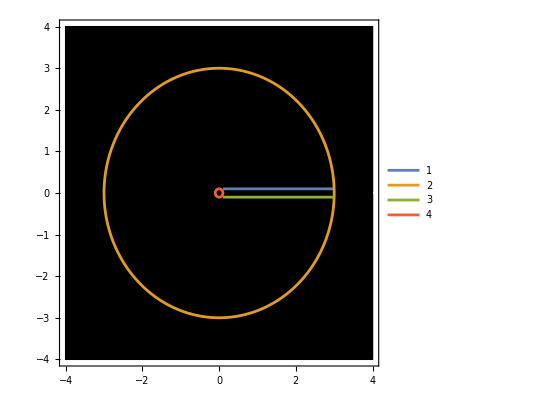

```mathematica
p1[t_]:=ϵ(1+ⅈ) + (R-ϵ)t 
p2[t_]:=R E^(2π ⅈ t)
p3[t_]:= R-ϵ ⅈ-(R-ϵ) t
p4[t_]:=ϵ E^(-2π ⅈ t)
α=-1.5;
{R,ϵ}={3,0.1};
Show[
ComplexPlot[f[α][z],{z,4}],
ParametricPlot[{ReIm[p1[t]],ReIm[p2[t]],ReIm[p3[t]],ReIm[p4[t]]},{t,0,1},
PlotLegends->Automatic]
]
```

We need to understand the jump across the branch cut. I need to compare
	f[x]=ⅇ^((α-1)(Log[-x]-ⅈ π))/(1+x)=ⅇ^((α-1)(Log[-(x + 0 ⅈ)]-ⅈ π))/(1+(x+ 0 ⅈ))
above the branch cut to the very similar expression below the branch cut
	ⅇ^((α-1)(Log[-(x - 0 ⅈ)]-ⅈ π))/(1+(x - 0 ⅈ))=ⅇ^((α-1)(Log[-x] +2π ⅈ - ⅈ π))/(1+x)=ⅇ^((α-1)(Log[-x] +π ⅈ))/(1+x)
tidy up the top to get
	ⅇ^((α-1)(Log[-(x - 0 ⅈ)]-ⅈ π))/(1+(x - 0 ⅈ))=(ⅇ^((α-1)(Log[-x] +π ⅈ))ⅇ^((α-1)π ⅈ))/(1+x)=ⅇ^((α-1)π ⅈ)f[x-0 ⅈ]
So we should have the expression

```mathematica
δ=0.00001;
α=0.4;
1/ⅇ^((α-1)2π ⅈ)
Table[(f[α][x+δ ⅈ])/(f[α][x-δ ⅈ]),{x,0.1,10,0.1}]
Table[(f[α][x+δ ⅈ])/(f[α][x]),{x,0.1,10,0.1}]
```

-0.809017-0.587785 ⅈ

{-0.809098-0.587673 ⅈ,-0.809062-0.587723 ⅈ,-0.80905-0.58774 ⅈ,-0.809043-0.587749 ⅈ,-0.809039-0.587755 ⅈ,-0.809036-0.587759 ⅈ,-0.809034-0.587762 ⅈ,-0.809032-0.587764 ⅈ,-0.809031-0.587766 ⅈ,-0.80903-0.587767 ⅈ,-0.809029-0.587769 ⅈ,-0.809028-0.58777 ⅈ,-0.809028-0.587771 ⅈ,-0.809027-0.587772 ⅈ,-0.809026-0.587772 ⅈ,-0.809026-0.587773 ⅈ,-0.809025-0.587774 ⅈ,-0.809025-0.587774 ⅈ,-0.809025-0.587775 ⅈ,-0.809024-0.587775 ⅈ,-0.809024-0.587775 ⅈ,-0.809024-0.587776 ⅈ,-0.809024-0.587776 ⅈ,-0.809023-0.587776 ⅈ,-0.809023-0.587777 ⅈ,-0.809023-0.587777 ⅈ,-0.809023-0.587777 ⅈ,-0.809023-0.587778 ⅈ,-0.809022-0.587778 ⅈ,-0.809022-0.587778 ⅈ,-0.809022-0.587778 ⅈ,-0.809022-0.587778 ⅈ,-0.809022-0.587779 ⅈ,-0.809022-0.587779 ⅈ,-0.809022-0.587779 ⅈ,-0.809022-0.587779 ⅈ,-0.809021-0.587779 ⅈ,-0.809021-0.587779 ⅈ,-0.809021-0.587779 ⅈ,-0.809021-0.58778 ⅈ,-0.809021-0.58778 ⅈ,-0.809021-0.58778 ⅈ,-0.809021-0.58778 ⅈ,-0.809021-0.58778 ⅈ,-0.809021-0.58778 ⅈ,-0.809021-0.58778 ⅈ,-0.809021-0.58778 ⅈ,-0.80902-0.58778 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587782 ⅈ,-0.80902-0.587782 ⅈ,-0.80902-0.587782 ⅈ,-0.80902-0.587782 ⅈ,-0.80902-0.587782 ⅈ,-0.80902-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ}

{-0.809058-0.587729 ⅈ,-0.80904-0.587754 ⅈ,-0.809033-0.587763 ⅈ,-0.80903-0.587767 ⅈ,-0.809028-0.58777 ⅈ,-0.809027-0.587772 ⅈ,-0.809025-0.587774 ⅈ,-0.809025-0.587775 ⅈ,-0.809024-0.587776 ⅈ,-0.809023-0.587776 ⅈ,-0.809023-0.587777 ⅈ,-0.809023-0.587778 ⅈ,-0.809022-0.587778 ⅈ,-0.809022-0.587778 ⅈ,-0.809022-0.587779 ⅈ,-0.809021-0.587779 ⅈ,-0.809021-0.587779 ⅈ,-0.809021-0.58778 ⅈ,-0.809021-0.58778 ⅈ,-0.809021-0.58778 ⅈ,-0.809021-0.58778 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587781 ⅈ,-0.80902-0.587782 ⅈ,-0.80902-0.587782 ⅈ,-0.80902-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587782 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809019-0.587783 ⅈ,-0.809018-0.587783 ⅈ,-0.809018-0.587783 ⅈ,-0.809018-0.587783 ⅈ,-0.809018-0.587783 ⅈ,-0.809018-0.587783 ⅈ,-0.809018-0.587783 ⅈ,-0.809018-0.587783 ⅈ,-0.809018-0.587783 ⅈ,-0.809018-0.587783 ⅈ,-0.809018-0.587783 ⅈ,-0.809018-0.587783 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ,-0.809018-0.587784 ⅈ}

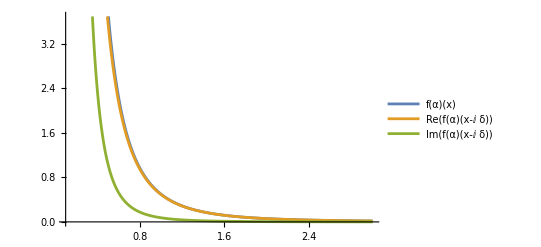

```mathematica
δ=0.05;
α=-1.5;
Plot[{f[α][x],Re[f[α][x-ⅈ δ]],Im[f[α][x-ⅈ δ]]},{x,ϵ,R},
PlotLegends->"Expressions"]
```

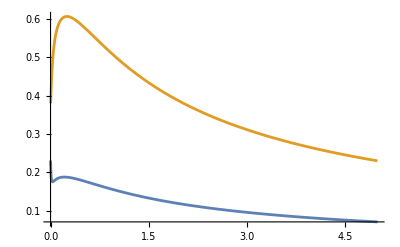

```mathematica
ϵ=0.01;
α=1.2;
Plot[ {
Re[ f[α][x+ϵ I]],
Re[ f[α][x-ϵ I]]
},{x, 0.0000001, 5}]
```